## Inicialize some functions

```mathematica
Remove["Global`*"]
```

```mathematica
<<CompiledFunctionTools`;
<<MaTeX`;
Needs["NumericalCalculus`"]
ParallelNeeds["NumericalCalculus`"]
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
compileOptionsPar={Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"};
font={BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize-> 12},BaseStyle->texStyle};
densityPlotOptions={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"};
```

## First order perturbation Hamiltonian

```mathematica
$Assumptions={λ∈Reals,χ∈Reals};
```

```mathematica
δ[a_,b_]:=KroneckerDelta[a,b];
Je[sn_,j_,m_]:=√(j(j+1)-m(m+sn 1));
```

```mathematica
V1[jp_,mp_,j_,m_]:=1/4(Je[1,j,m+1]Je[1,j,m]δ[mp,m+2]+Je[-1,j,m-1]Je[-1,j,m]δ[mp,m-2]+δ[mp,m](Je[-1,j,m]Je[1,j,m-1]+Je[1,j,m]Je[-1,j,m+1] ))
V2[jp_,mp_,j_,m_]:=1/2(m+j)(Je[1,j,m]δ[mp,m+1]+Je[-1,j,m]δ[mp,m-1])+1/2(m+1+j)Je[1,j,m]δ[mp,m+1]+1/2(m-1+j)Je[-1,j,m]δ[mp,m-1]
V3[jp_,mp_,j_,m_]:=δ[mp,m](j+m)^2
Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]-δ[jp,j]/(2j)(λ V1[jp,mp,j,m]+χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m])
```

```mathematica
nn=5;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

```mathematica
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,en,eigNonSort,eig,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig⟦1⟧].DH1C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1C[λ,χ].eig⟦1⟧&/@Range[2,dim];

M2=Conjugate[eig⟦1⟧].DH2C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2C[λ,χ].eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];
g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

# Geodesics vs. lines

```mathematica
(*geodbg=DensityPlot[Det@gC[λ,χ],{λ,-0.3,1.2},{χ,0,0.9},Evaluate@densityPlotOptions,ScalingFunctions->"Log10",PlotPoints->150];
Export[NotebookDirectory[]<>"savedData/geodbg_N=5.m",geodbg]*)
```

```mathematica
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
groundState[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig,eigNon,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
eig⟦1⟧
]
```

```mathematica
path=Import[NotebookDirectory[]<>"savedData/solMulti_N=5_maxtheta=1.m"];
```

```mathematica
geodbg=DensityPlot[Det@gC[λ,χ],{λ,-0.3,1.5},{χ,0,1},Evaluate@densityPlotOptions,ScalingFunctions->"Log10",PlotPoints->150];
```

```mathematica
paths=Map[Flatten,{λ,χ}/.path];
```

```mathematica
numPaths=Dimensions[paths]⟦1⟧;
```

```mathematica
endTimes=paths⟦#,1,1,1,2⟧&/@Range[Dimensions[paths]⟦1⟧]
```

{10.,9.21984,8.45755,8.01436,7.97566,7.94704,7.92302,7.90276,7.88602,7.87271,7.86274,7.85606,7.85262,7.8524,7.85541,7.8617,7.87133,7.88445,7.90122,7.92191,7.94686,7.97655,8.01167,8.05328,8.10294,8.16227,8.32045,10.,10.,10.,10.,10.,8.06372,7.87824,7.77922,7.72391,7.66581,7.69766,10.,7.41637,7.44411,7.48848,7.91252,8.58814,10.,10.,10.,10.,10.,10.,10.}

```mathematica
geodInitial=ParametricPlot[{λ[t],χ[t]}/.path⟦#⟧,{t,0,endTimes⟦#⟧},PlotRange->All,Frame->True,PlotStyle->Green]&/@Range[numPaths];
Show[{geodbg,geodInitial}]
```

-Graphics-

```mathematica
tmaxM=Min[endTimes]
{λin,χin}={0,0};
num=500;
fin=Map[Flatten,{λ[#],χ[#]}/.path]&/@Range[tmaxM/num,tmaxM,tmaxM/num];
line[tt_,j_]:=Module[{λfinal,χfinal},
{λfinal,χfinal}=Flatten[{λ[tt],χ[tt]}/.path⟦j⟧];
{{λ[t]->λin+((λfinal-λin)t)/tt,χ[t]->χin+((χfinal-χin)t)/tt,λ'[t]->(λfinal-λin)/tt,χ'[t]->(χfinal-χin)/tt}}];
```

7.41637

```mathematica
Dimensions@fin
```

{500,51,2}

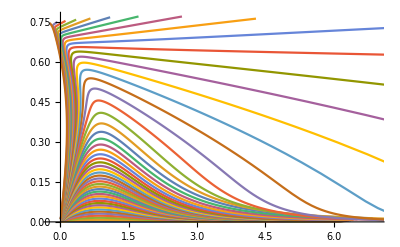

```mathematica
ListLinePlot[Transpose@fin]
```

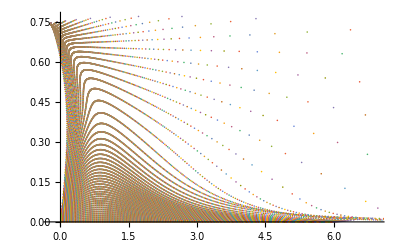

```mathematica
ListPlot[fin]
```

```mathematica
parLine=ParametricPlot[Map[{λ[t],χ[t]}/.line[5,#]&,Range[numPaths]],{t,0,5},PlotStyle->Orange,PlotLegends->{"Dline"}];
```

```mathematica
parPath=ParametricPlot[{λ[t],χ[t]}/.path,{t,0,tmaxM},PlotLegends->{"Dpath"}];
```

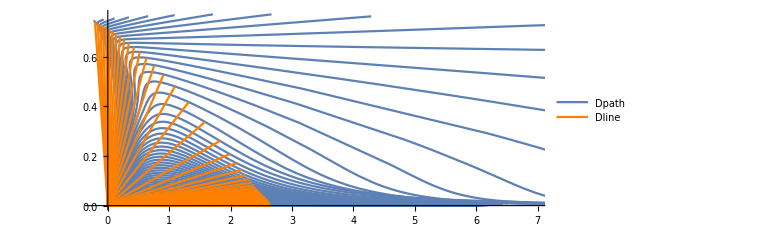

```mathematica
Show[{parPath,parLine},ImageSize->Large]
```

## Distance

```mathematica
L=√({λ'[t],χ'[t]}.gC[λ[t],χ[t]].{λ'[t],χ'[t]});
numD=10;
Dstep=tmaxM/numD;
```

```mathematica
DtMax=7;
```

```mathematica
Dline=Flatten@Map[NIntegrate[L/.line[DtMax,#],{t,0,DtMax}]&,Range[numPaths]];
```

```mathematica
Dpath=Flatten@NIntegrate[L/.path,{t,0,DtMax}];
```

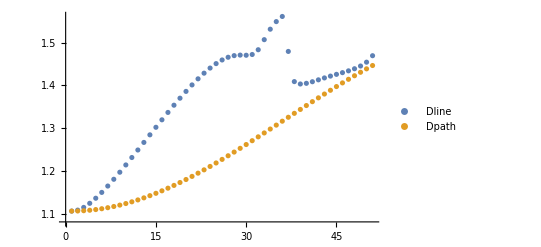

```mathematica
ListPlot[{Dline,Dpath},PlotLegends->{"Dline","Dpath"}]
```

```mathematica
DlineM=Table[Flatten@Map[NIntegrate[L/.line[t1,#],{t,0,t1}]&,Range[numPaths]],{t1,Dstep,tmaxM-Dstep,Dstep}];
```

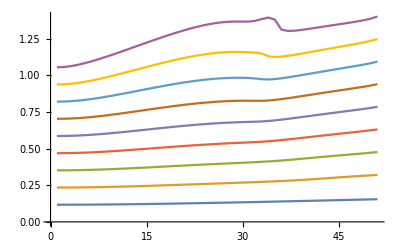

```mathematica
ListLinePlot[DlineM]
```

```mathematica
DpathM=Accumulate@Table[Flatten@NIntegrate[L/.path,{t,t1,t1+Dstep}],{t1,Dstep,tmaxM-Dstep,Dstep}];
```

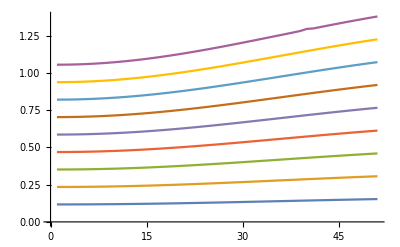

```mathematica
ListLinePlot[DpathM]
```

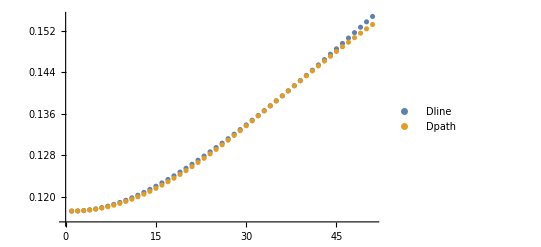
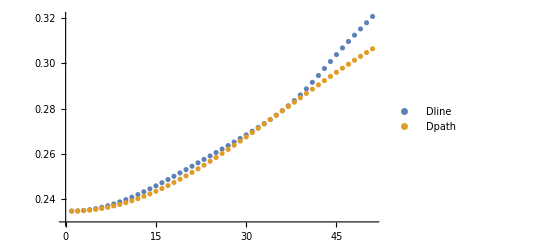
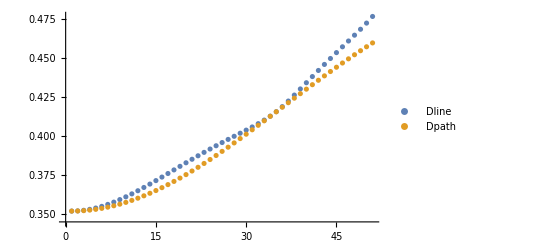
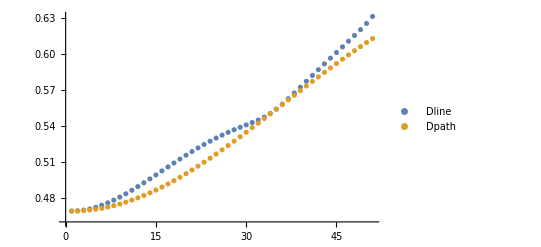
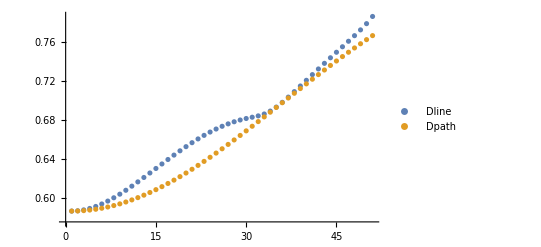
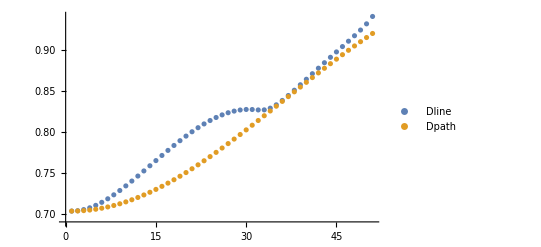
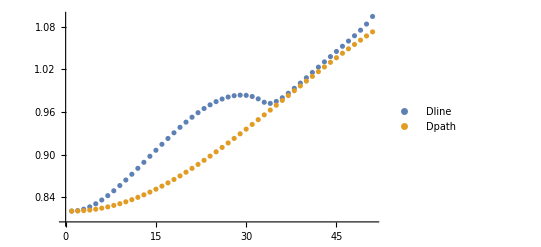
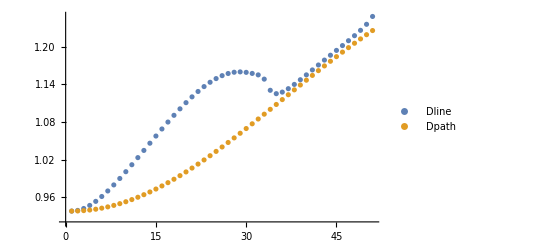

```mathematica
ListPlot[{DlineM⟦#⟧,DpathM⟦#⟧},PlotLegends->{"Dline","Dpath"}]&/@Range[numD-1]
```

## Fidelity

```mathematica
F=(Conjugate[ND[groundState[l,χ[t]],l,λ[t]]]λ'[t]+Conjugate[ND[groundState[λ[t],c],c,χ[t]]]χ'[t]).groundState[λ[t],χ[t]];
numF=10;
Fstep=tmaxM/numF;
```

```mathematica
FlineM=Table[Flatten@Map[Quiet@NIntegrate[F/.line[t1,#],{t,0,t1}]&,Range[numPaths]],{t1,Fstep,tmaxM-Fstep,Fstep}];
```

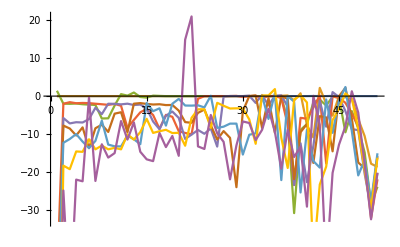

```mathematica
ListLinePlot[FlineM]
```

```mathematica
FpathM=Table[Flatten@NIntegrate[F/.path⟦#⟧,{t,t1,t1+Fstep}],{t1,Fstep,tmaxM-Fstep,Fstep}]&/@Range[30,numPaths];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.950836030290849}. NIntegrate obtained -0.000045718 and 9.02396×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.78533}. NIntegrate obtained 0.184764 and 0.0000344127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.07593}. NIntegrate obtained 0.066051 and 0.0000521483 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

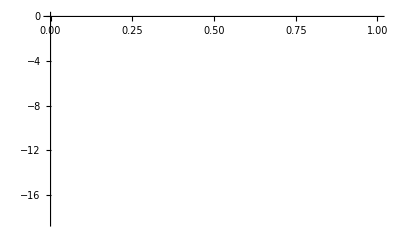

```mathematica
ListLinePlot[FpathM]
```

```mathematica
ListPlot[{FlineM⟦#⟧,FpathM⟦#⟧},PlotLegends->{"Fline","Fpath"}]&/@Range[numF-1]
```

ReplaceAll::reps: {line[t1,numPaths]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::nlim: t = t1 is not a valid limit of integration.

ReplaceAll::reps: {line[t1,numPaths]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::nlim: t = t1 is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

Range::range: Range specification in Range[NIntegrate[F/.line[t1,numPaths],{t,0,t1}]] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

$Aborted

## Energy variation

```mathematica
δE2=Conjugate[groundState[λ[t],χ[t]]].MatrixPower[H[λ[t],χ[t]],2].groundState[λ[t],χ[t]]-(Conjugate[groundState[λ[t],χ[t]]].H[λ[t],χ[t]].groundState[λ[t],χ[t]])^2;
```

```mathematica
Estep=tmaxM/100;
```

```mathematica
Eline=Quiet@Flatten@Table[1/Estep NIntegrate[δE2/.line,{t,t1,t1+Estep}],{t1,0,tmaxM-Estep, Estep}];
```

.14me

```mathematica
Epath=Quiet@Flatten@Table[1/Estep NIntegrate[δE2/.path,{t,t1,t1+Estep}],{t1,0,tmaxM-Estep, Estep}];
```

```mathematica
ListLinePlot[{Eline,Epath}]
```